```mathematica
Integrate[1/(2 √x),{x,0,1}]
```

1

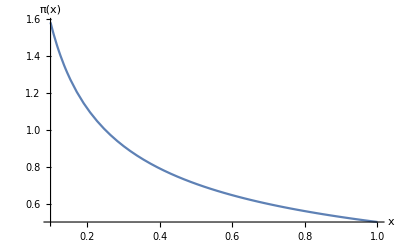

```mathematica
PiDist[x_]:=1/(2 √x);
Plot[PiDist[x],{x,0.1,1},AxesLabel->{"x","π(x)"}]
```

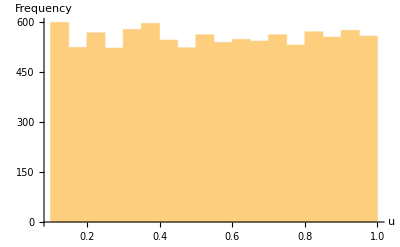

```mathematica
u=RandomVariate[UniformDistribution[{0.1,1}],10000];
Histogram[u,AxesLabel->{"u", "Frequency"}]
```

```mathematica
FInverse[u_]:=(1/(2u))^2
```

```mathematica
sample=FInverse[u];
```

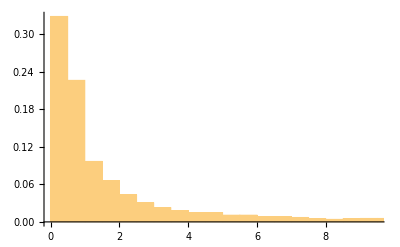

```mathematica
Histogram[sample,Automatic,"Probability", AxesLabel->Automatic]
```